```mathematica
(*Same idea of TrAmu_complete_XX_v2, but with an attempt of parallelizing the code*)
```

```mathematica
(*Legendre associated polynomial function. Also in this case we need to check |m|<=j*)
LGP[j_,m_,θ_]:=If [Abs[m]<=j, √((2 j+1)/(4π)((j-m)!)/((j+m)!))LegendreP[j,m,Cos[θ]], 0]

(*Clebsh-Gordan function*)
CG[j_,m_,n_,J_,M_]:=If[m+n==M &&Abs[M]<=J,
ClebschGordan[{j,m},{j,n},{J,M}],
0
]

(*Ladder operators. Necessary the checks Abs[m]<=j, otherwise it returns an imaginary number*)
(*For the formulas see Wikipedia*)

Cplus[j_,m_]  :=If [Abs[m]<=j, √((j-m)×(j-m+1)), 0]
Cminus[j_,m_]:=If [Abs[m]<=j, √((j+m)×(j-m+1)), 0]
```

```mathematica
(*Integrals Section*)
(*φ integral when O=Subscript[Z, 1] Subscript[Z, 2]*)
IntZZ[m_, n_] := Module[{numerator,denominator, result},
If [m==n, result = 0,

(*otherwise, if m≠n*)
numerator = ⅈ (-1+ⅇ^(ⅈ (-m+n)π/2))^3 (1+ⅇ^(ⅈ (-m+n)π/2));
denominator = m-n;

result = numerator/denominator];

result // Chop
]

(*φ integral when O=Subscript[X, 1] Subscript[X, 2] on φ register*)
IntXX[m_,n_]:=Module[{numerator,denominator,result},
If[m==n,result=1/2 ⅇ^(-3/2 ⅈ m π) (1+ⅇ^(ⅈ m π)+ⅇ^(2 ⅈ m π)+ⅇ^(3 ⅈ m π)) π,

(*otherwise, if m≠n*)
result=-1/(m-n)ⅈ ⅇ^(-2 ⅈ m π) (ⅇ^((ⅈ m π)/2)-ⅇ^((ⅈ n π)/2)+ⅇ^(1/2 ⅈ (2 m+n) π)-ⅇ^(1/2 ⅈ (m+2 n) π)+ⅇ^(1/2 ⅈ (3 m+2 n) π)-ⅇ^(1/2 ⅈ (2 m+3 n) π)+ⅇ^(1/2 ⅈ (4 m+3 n) π)-ⅇ^(1/2 ⅈ (3 m+4 n) π));
];

result // Chop
]


ClearAll[Integral]

(*Define a cache to memorize the results of the integrals*)
integralCache=<||>;

(*Function to calculate the integral with caching*)
Integral[j_,m_,n_]:=Module[{key,result},

(*Generate a unique key for  and *)
key=Sort[{m,n}];

(*If the integral is already calculated, it's recovered in the cache*)
If[KeyExistsQ[integralCache,key],

result=integralCache[key],

(*Otherwise it calculates the integral and it memorize in the cache*)
If[Abs[m]>j||Abs[n]>j,Return[0]];

integralPhi=IntXX[m,n];

If[integralPhi==0,
result=0,
integralTheta=NIntegrate[LGP[j,m,θ]*LGP[j,n,θ]*Sin[θ],{θ,0,π}];

result=Chop[integralPhi*integralTheta]
];

(*memorize in the cache*)
integralCache[key]=result;];

result
]

(*Define a parallel version of the Integral function*)
ParallelIntegral[j_,m_,n_]:=Parallelize[Integral[j,m,n]]
```

```mathematica
(*Approximated version of Subscript[Tr, J][Subscript[A, μ]] by taking only m>n*)
ClearAll[TrAxComplete];

TrAxComplete[j_,J_]:=Module[{sumM,result,cgm1,cgm2,term,timing},
If[J>2*j,Return[{0,0}]];

timing=AbsoluteTiming[
sumM=Sum[
If[Abs[M-m]<=j&&Abs[M-n]<=j&&n>m,(*Aggiunta del vincolo n>m*)
cgm1=CG[j,m,M-m,J,M];
cgm2=CG[j,n,M-n,J,M];
If[cgm1!=0&&cgm2!=0,term=Cplus[j,M-m]*Integral[j,M-m+1,M-n]+Cminus[j,M-m]*Integral[j,M-m-1,M-n]-Cplus[j,M-n]*Integral[j,M-m,M-n+1]-Cminus[j,M-n]*Integral[j,M-m,M-n-1];

If[term!=0,cgm1*cgm2*term*(Cplus[j,m]*Integral[j,m+1,n]+Cminus[j,m]*Integral[j,m-1,n]-Cplus[j,n]*Integral[j,m,n+1]-Cminus[j,n]*Integral[j,m,n-1]),0],0],0],{M,-J,J},{m,-j,j},{n,-j,j}];

result=(1/2)*sumM;
Chop[result]][[1]];

result=Chop[result];
Return[{result,timing}];
]




(*Approximated version of Subscript[Tr, J][Subscript[A, μ]] by taking only m>n*)
ClearAll[TrAxReduced];

TrAxReduced[j_,J_]:=Module[{sumM,result,cgm1,cgm2,term,timing},If[J>2*j,Return[{0,0}]];
timing=AbsoluteTiming[sumM=Sum[If[M==2*j-2&&m==j&&n==j-1,(*Condizione aggiunta*)If[Abs[M-m]<=j&&Abs[M-n]<=j&&n>m,(*Aggiunta del vincolo n>m*)cgm1=CG[j,m,M-m,J,M];
cgm2=CG[j,n,M-n,J,M];
If[cgm1!=0&&cgm2!=0,term=Cplus[j,M-m]*Integral[j,M-m+1,M-n]+Cminus[j,M-m]*Integral[j,M-m-1,M-n]-Cplus[j,M-n]*Integral[j,M-m,M-n+1]-Cminus[j,M-n]*Integral[j,M-m,M-n-1];
If[term!=0,cgm1*cgm2*term*(Cplus[j,m]*Integral[j,m+1,n]+Cminus[j,m]*Integral[j,m-1,n]-Cplus[j,n]*Integral[j,m,n+1]-Cminus[j,n]*Integral[j,m,n-1]),0],0],0],0],{M,-J,J},{m,-j,j},{n,-j,j}];
result=(1/2)*sumM;
Chop[result]][[1]];
result=Chop[result];
Return[{result,timing}];]
```

```mathematica
nQubs=6;
jj = 4;(*jj=2^(nQubs-1);*)
JJValues=Range[0,2*jj];

(*Placeholder per la funzione di timing-da sostituire con la funzione reale*)
TimingFunction[expr_]:=First@Timing[expr];

(*Definizione della funzione per formattare i risultati*)
formatHeader[jj_,totalTiming_]:="j = "<>ToString[jj]<>"\n"<>"timing = "<>ToString[totalTiming]<>"\n"<>"J\tTrValue\tTiming\n";

formatResult[JJ_,result_,timing_]:=ToString[JJ]<>"\t"<>ToString[result,InputForm]<>"\t"<>ToString[timing,InputForm]<>"\n";

(*Calcolo dei risultati e dei tempi totali in un'unica passata*)
results=Table[Module[{result,timing},{result,timing}=TrAxComplete[jj,JJ];
{JJ,result,timing}],{JJ,JJValues}];

(*Total sum of compilation times at fixed jj*)
totalTiming=Total[results[[All,3]]]; 

(*Results formattation*)
formattedResults=StringJoin[formatResult[#[[1]],#[[2]],#[[3]]]&/@results];

(*Creazione della tabella di risultati formattati con il totale del timing*)
formattedResults=formatHeader[jj,totalTiming]<>formattedResults;

(*Output directory definition*)
outputDir="C:\\Users\\meleg\\OneDrive\\Desktop\\Mathematica\\results_TrAmu_complete";

(*Creazione dinamica del nome del file basato sul valore di jj*)
outputFileName=StringTemplate["results_TrAmu_j=`jj`.txt"][<|"jj"->ToString[jj]|>];

(*Combinazione della directory e del nome del file*)
outputPath=FileNameJoin[{outputDir,outputFileName}];

(*Esportazione dei risultati formattati nel file dinamico*)
Export[outputPath,formattedResults,"Text"];

Print["Results saved to ",outputFileName," in ",outputDir];
```

Results saved to results_TrAmu_j=4.txt in C:\Users\meleg\OneDrive\Desktop\Mathematica\results_TrAmu_complete

```mathematica
(*Plot section*)

jj=32;
(*Directory to plot data*)
outputDir="C:\\Users\\meleg\\OneDrive\\Desktop\\Mathematica\\results_TrAmu_complete";

outputFileName=StringTemplate["results_TrAmu_j=`jj`.txt"][<|"jj"->ToString[jj]|>];
outputPath=FileNameJoin[{outputDir,outputFileName}];

(*Lettura dei dati dal file*)
data=Import[outputPath,"Text"];

(*Parsing dei dati*)
(*Rimuovere la prima riga di intestazione e quella con il totale del timing*)
lines=StringSplit[data,"\n"];
headerLine=First[lines]; (*La riga dell'intestazione*)
timingLine=lines[[2]]; (*La riga con il timing totale*)
dataLines=Rest[Rest[Rest[lines]]]; (*Rimuove le prime due righe*)

(*Parsing dei dati rimanenti*)
parsedData=StringSplit[#,{"\t","=","\n"}]&/@dataLines;

(*Filtra le righe valide e prepara i dati per i grafici*)
parsedData=Select[parsedData,Length[#]==3&]; (*Cambiato a 3 in base alla riga del formato*)

(*Estrai i valori*)
JValues=ToExpression[#[[1]]]&/@parsedData;
TrValues=ToExpression[#[[2]]]&/@parsedData;
TimingValues=ToExpression[#[[3]]]&/@parsedData;

Print[TrValues]

(*Creazione del plot corretto di TrValue in funzione di J*)
trValuePlot=ListPlot[Transpose[{JValues,TrValues}],PlotMarkers->Automatic,PlotStyle->{Blue,PointSize[Medium]},Joined->True,AxesLabel->{"J","TrValue"},PlotLabel->"TrValue vs J",GridLines->Automatic];

(*Creazione del plot corretto di Timing in funzione di J*)
timingPlot=ListPlot[Transpose[{JValues,TimingValues}],PlotMarkers->Automatic,PlotStyle->{Red,PointSize[Medium]},Joined->True,AxesLabel->{"J","Timing (s)"},PlotLabel->"Timing vs J",GridLines->Automatic];

(*Mostrare i plot*)
trValuePlot
timingPlot
```

Import::nffil: File C:\Users\meleg\OneDrive\Desktop\Mathematica\results_TrAmu_complete\results_TrAmu_j=32.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,
].

Rest::norest: Cannot take Rest of expression {} with length zero.

Rest::argx: Rest called with 0 arguments; 1 argument is expected.

Rest[]

-Graphics-

-Graphics-

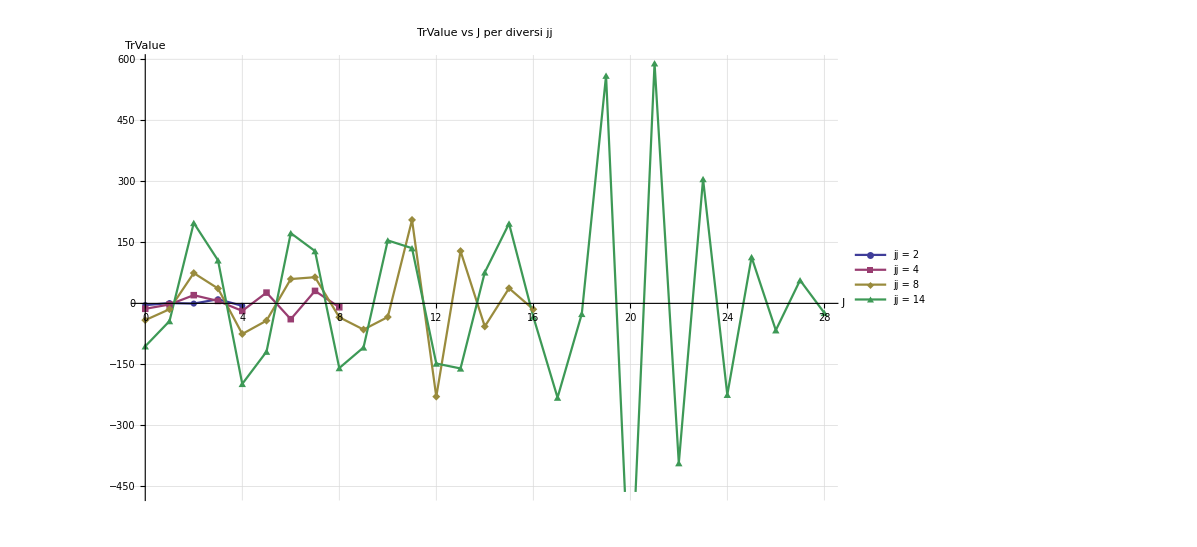

```mathematica
(*Plot section*)jjValues={2,4,8,14};

(*Directory to plot data*)
outputDir="C:\\Users\\meleg\\OneDrive\\Desktop\\Mathematica\\results_TrAmu_complete";

(*Inizializzare una lista per contenere i dati da plottare*)
allTrValues={};
allJValues={};
legends={};

(*Loop attraverso tutti i valori di jj*)
Do[((*Genera il nome del file per il valore corrente di jj*)outputFileName=StringTemplate["results_TrAmu_j=`jj`.txt"][<|"jj"->ToString[jj]|>];
outputPath=FileNameJoin[{outputDir,outputFileName}];
(*Lettura dei dati dal file*)data=Import[outputPath,"Text"];
(*Parsing dei dati*)(*Rimuovere la prima riga di intestazione e quella con il totale del timing*)lines=StringSplit[data,"\n"];
dataLines=Rest[Rest[Rest[lines]]];(*Rimuove le prime tre righe*)(*Parsing dei dati rimanenti*)parsedData=StringSplit[#,{"\t","=","\n"}]&/@dataLines;
(*Filtra le righe valide e prepara i dati per i grafici*)parsedData=Select[parsedData,Length[#]==3&];
(*Estrai i valori*)JValues=ToExpression[#[[1]]]&/@parsedData;
TrValues=ToExpression[#[[2]]]&/@parsedData;
(*Aggiungi i valori a tutte le liste*)AppendTo[allTrValues,TrValues];
AppendTo[allJValues,JValues];
AppendTo[legends,"jj = "<>ToString[jj]];),{jj,jjValues}]

(*Creazione del plot di TrValue per tutti i jj*)
trValuePlot=ListLinePlot[Table[Transpose[{allJValues[[i]],allTrValues[[i]]}],{i,Length[jjValues]}],PlotMarkers->Automatic,PlotStyle->Table[ColorData[1][i],{i,Length[jjValues]}],Joined->True,AxesLabel->{"J","TrValue"},PlotLabel->"TrValue vs J per diversi jj",GridLines->Automatic,PlotLegends->legends];

(*Mostrare il plot*)
trValuePlot
```